Direct  unconstrained estimates of tetrad classes (Er) across a range of B values (plot and table).
Analytical estimates of Er (r,  number of crossovers in a tetrad) based on the observed number of crossover (CO) classes based on Weinstein’s eqs. (1936), modified to allow for meiotic drive (B) during meiosis II based on different number of 
crossovers between sister chromatids, following Pettie et al. (2022). B (0 ⩽ B ⩽ 1)  indicates the probability of a chromatid with more crossovers that its sister to be included into the oocyte. B = 0.5 is equivalent to Weinstein’s model. B > 0.5 (B<0.5) allows preferential inclusion into oocytes of chromatids with more (fewer) crossovers relative to their sister chromatid. 
The results can be used to identify the range of B values that generate biologically feasible Er values (1 ⩽ Er ⩽ 0).

Citations:
- Weinstein, A. 1936. The theory of multiple-strand crossing over. Genetics 21:155–199
- Pettie, N., et al. 2022. Meiotic, genomic and evolutionary properties of crossover distribution in Drosophila yakuba. PLOS Genetics 8(3):e1010087.doi:10.1371/journal.pgen.1010087
- Llopart et a. 2025. A high-resolution crossover landscape in Drosophila santomea reveals rapid and concerted evolution of multiple properties of crossing-over control. PLOS Genetics

Plot E-values_vs_B

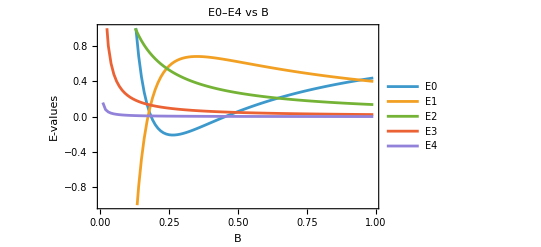

Saved file: E-values_vs_B.csv

C:\Users\jcomeron\Documents\ML-Weinsteon-2025\E-values_vs_B.csv

```mathematica
(*=== INPUT data below ===*)
(* Observed number of crossover classes (NCO, no crossovers; CO1, 1 crossover; CO2, 2 crossovers...)*) 
(* Bmin/Bmax: Range for B, bias during segregation of sister chromatids towards the oocyte based on different number of crossovers *)
NCO=1015;CO1=1013;CO2=256;CO3=32;CO4=6;
NCO=2212;CO1=2318;CO2=432;CO3=34;CO4=1;
Bmin=0.01; Bmax=0.99; Bstep=0.01;

(*=== Options, Variables and Equation System ===*)
SetOptions[EvaluationNotebook[],WorkingPrecision->50,ShowCellLabel->False];
observed={NCO,CO1,CO2,CO3,CO4};
T=Total[observed];
vars={E0,E1,E2,E3,E4};
eqns[B_]:={E0+(1-B) E1+1/2 (1-B) E2+1/4 (1-B) E3+1/8 (1-B) E4==NCO/T,B E1+1/2 E2+3/4 (1-B) E3+4/8 (1-B) E4==CO1/T,1/2 B E2+3/4 B E3+3/8 E4==CO2/T,1/4 B E3+1/2 B E4==CO3/T,1/8 B E4==CO4/T};

(*=== Solve System for Each B ===*)
results=Table[sol=Quiet[NSolve[eqns[b],vars]];
If[Length[sol]>0,{b,E0,E1,E2,E3,E4}/. sol[[1]],Nothing],{b,Bmin,Bmax,Bstep}];

(*=== Prepare for Plot and Plot ===*)
{bVals,e0Vals,e1Vals,e2Vals,e3Vals,e4Vals}=Transpose[results];
YVals=Join[e0Vals,e1Vals,e2Vals,e3Vals,e4Vals];
yMin=Min[YVals]; yMax=Max[YVals]; yRange=If[yMin<-0.95||yMax>0.95,{-1,1},Automatic];
Style["Plot E-values_vs_B",Bold,Red]
ListLinePlot[{Transpose[{bVals,e0Vals}],Transpose[{bVals,e1Vals}],Transpose[{bVals,e2Vals}],Transpose[{bVals,e3Vals}],Transpose[{bVals,e4Vals}]},PlotLegends->{"E0","E1","E2","E3","E4"},Joined->True,Frame->True,FrameLabel->{"B","E-values"},PlotLabel->"E0–E4 vs B",PlotMarkers->None,AxesOrigin->{0.5,0},PlotRange->{All,yRange}]

(* === Export Table ===*)
Style["Saved file: E-values_vs_B.csv",Bold,Red]
ExportPath=FileNameJoin[{NotebookDirectory[],"E-values_vs_B.csv"}];
Export[ExportPath,Prepend[results,{"B","E0","E1","E2","E3","E4"}]]
Quit[]
```